```mathematica
filename="/home/anegi/August/3-Aug-19-09-49/Î»_list/Î»_positive"
data= Import[filename,"Table",FieldSeparators->","];
Ly= {10,14,20,28,40,56,80};
MatrixLy=Table[ConstantArray[Ly[[i]],Dimensions[data][[2]]],{i,Length[Ly]}];
gamma= Table[Log10[data[[i,j]]*MatrixLy[[i,j]]],{i,Dimensions[data][[1]]},{j,Dimensions[data][[2]]}];
(*ERRORgamma= Table[0.434*ERRORdata[[i,j]]/data[[i,j]],{i,Dimensions[ERRORdata][[1]]},{j,Dimensions[ERRORdata][[2]]}];*)

Wd=N@Subdivide[-0.05,0.05,19]; (* here actually we are scanning over m*)
(*Wc=2.17;

MatrixWd=Table[Wd,{i,8}];*)
(*MatrixWd=Table[(Wd-Wc)/Wc,{i,Length[Ly]}]*)
MatrixWd=Table[Wd,{i,Length[Ly]}];
start=1;
stop=20;
(*errors=Flatten[ERRORgamma[[1;;Length[Ly],start;;stop]]];*)
FitData=Transpose[{Flatten[MatrixWd[[1;;Length[Ly],start;;stop]]],Flatten[MatrixLy[[1;;Length[Ly],start;;stop]]],Flatten[gamma[[1;;Length[Ly],start;;stop]]]}];
vlist={};
xclist={};

Wc=0.00001
```

/home/anegi/August/3-Aug-19-09-49/Î»_list/Î»_positive

0.00001

```mathematica
Dimensions[FitData]
```

{140,3}

```mathematica
u0[x]=(x-xc)/xc ;
u1[x]=0;

T[x,M]=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3+ T4*(u0[x]*M^(1/v))^4+ T5*(u0[x]*M^(1/v))^5+ T6*(u0[x]*M^(1/v))^6;

model1=T0+T1*u0[x]*M^(1/v) ;
model2=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 ;
model3=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3;
model4=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3+ T4*(u0[x]*M^(1/v))^4;
model5=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3+ T4*(u0[x]*M^(1/v))^4+ T5*(u0[x]*M^(1/v))^5;
model6=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3+ T4*(u0[x]*M^(1/v))^4+ T5*(u0[x]*M^(1/v))^5+ T6*(u0[x]*M^(1/v))^6;
model7=T0+T1*u0[x]*M^(1/v) + T2*(u0[x]*M^(1/v))^2 + T3*(u0[x]*M^(1/v))^3+ T4*(u0[x]*M^(1/v))^4+ T5*(u0[x]*M^(1/v))^5+ T6*(u0[x]*M^(1/v))^6+T7*(u0[x]*M^(1/v))^7;
```

```mathematica
Simplify[model]
Expand[model]
Collect[model,x]
```

model

model

model

```mathematica
T0-M^(1/v) T1+(M^(1/v) T1 x)/xc
```

T0-M^(1/v) T1+(M^(1/v) T1 x)/xc

```mathematica
FitData;
```

```mathematica
fit1=NonlinearModelFit[FitData,{model1},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit2=NonlinearModelFit[FitData,{model2},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit3=NonlinearModelFit[FitData,{model3},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit4=NonlinearModelFit[FitData,{model4},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit5=NonlinearModelFit[FitData,{model5},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit6=NonlinearModelFit[FitData,{model6},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{a1,0.01}},{x,M}]
fit7=NonlinearModelFit[FitData,{model7},{{xc,Wc}, {v,1.0},{T0,0.18},{T1,0.18},{T2,-1.0},{T3,-1.0},{T4,-1.0},{T5,-1.0},{T6,-1.0},{T7,-1.0},{a1,0.01}},{x,M}]
```

FittedModel[0.182598-0.180847 M^1.00208 (0.0049111+x)]

FittedModel[0.160629-0.174645 M^1.01956 (-0.00300449+x)-0.0151494 M^2.03913 (-0.00300449+x)^2]

FittedModel[0.160619-0.188413 M^0.995518 (-0.00314425+x)-0.0191551 M^1.99104 (-0.00314425+x)^2-0.000671371 M^2.98655 (-0.00314425+x)^3]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.164877-0.188682 M^0.994766 (-0.00242882+x)-0.0186124 M^1.98953 (-«22»+x)^2-0.000485547 M^2.9843 (-0.00242882+x)^3+0.0000559317 M^3.97906 (-0.00242882+x)^4]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.174589-0.207579 M^0.958894 (-0.000258954+x)-0.0198715 M^1.91779 (-«23»+x)^2-«22» M^(«18») («1»)^3-0.000193714 M^3.83557 (-0.000258954+x)^4+0.0000990621 M^4.79447 (-0.000258954+x)^5]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.173689-0.211773 M^0.952218 (-0.0000555672+x)-0.0136394 M^1.90444 (-«23»+x)^2-«22» M^(«18») («1»)^3-«1»+0.000160275 M^4.76109 (-0.0000555672+x)^5+0.000176235 M^5.71331 (-0.0000555672+x)^6]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.173704-0.21181 M^0.951643 (-0.000052377+x)-0.0136843 M^1.90329 (-«24»+x)^2-«1»-«1»+«22» M^(«18») («1»)^5+0.000179062 M^5.70986 (-0.000052377+x)^6-6.43536×10^-6 M^6.6615 (-0.000052377+x)^7]

{0.997923,0.980811,1.0045,1.00526,1.04287,1.05018}

{-0.0049111,0.00300449,0.00314425,0.00242882,0.000258954,0.0000555672}

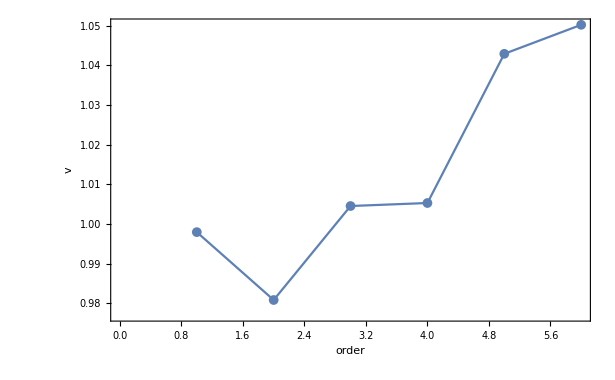

plot_v.jpg

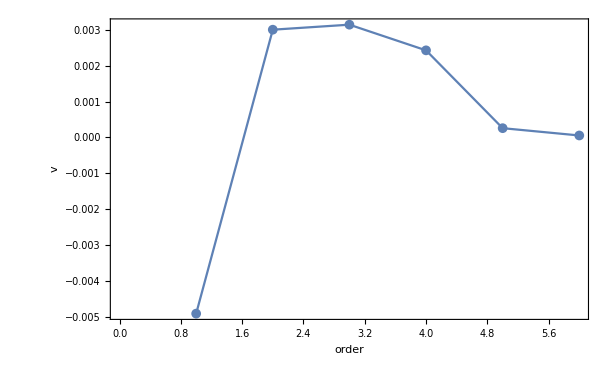

plot_xc.jpg

```mathematica
(*comparing different models for fitting*)
vlist={v/.fit1["BestFitParameters"],v/.fit2["BestFitParameters"],v/.fit3["BestFitParameters"],v/.fit4["BestFitParameters"],v/.fit5["BestFitParameters"],v/.fit6["BestFitParameters"]}
xclist={xc/.fit1["BestFitParameters"],xc/.fit2["BestFitParameters"],xc/.fit3["BestFitParameters"],xc/.fit4["BestFitParameters"],xc/.fit5["BestFitParameters"],xc/.fit6["BestFitParameters"]}
g20=ListLinePlot[vlist,AxesLabel->"v",ImageSize->Medium,PlotMarkers->{Automatic, 10},Frame-> True, FrameLabel->{HoldForm[order],HoldForm[v]},PlotLabel->None,LabelStyle->{FontFamily->"Albany",12,GrayLevel[0]}]
Export["plot_v.jpg",g20]

g21=ListLinePlot[xclist,AxesLabel->"xc",ImageSize->Medium,PlotMarkers->{Automatic, 10},Frame-> True, FrameLabel->{HoldForm[order],HoldForm[v]},PlotLabel->None,LabelStyle->{FontFamily->"Albany",12,GrayLevel[0]}]
Export["plot_xc.jpg",g21]
```

```mathematica
fitt=fit4
fitt["ParameterTable"]
fitt["BestFit"]
myv=v/.fitt["BestFitParameters"];
myxc=xc/.fitt["BestFitParameters"];
myT0=T0/.fitt["BestFitParameters"];/home/anegi/RESULT_scale3_2019-07-17T22:36:13.561/
myT1=T1/.fitt["BestFitParameters"];
myT2=T2/.fitt["BestFitParameters"];
myT3=T3/.fitt["BestFitParameters"];
myT4=T4/.fitt["BestFitParameters"];

(*AppendTo[vlist,myv]
AppendTo[xclist,myxc]*)
```

FittedModel[0.164877-0.188682 M^0.994766 (-0.00242882+x)-0.0186124 M^1.98953 (-«22»+x)^2-0.000485547 M^2.9843 (-0.00242882+x)^3+0.0000559317 M^3.97906 (-0.00242882+x)^4]

| Estimate | Standard Error | t-Statistic | P-Value
xc | 0.00242882 | 0.000219408 | 11.0699 | 1.78785×10^-20
v | 1.00526 | 0.00909318 | 110.551 | 1.95364×10^-130
T0 | 0.164877 | 0.00130492 | 126.351 | 6.57787×10^-138
T1 | -0.000458276 | 0.0000411248 | -11.1435 | 1.17107×10^-20
T2 | -1.09798×10^-7 | 2.202×10^-8 | -4.98628 | 1.9287×10^-6
T3 | -6.95695×10^-12 | 3.22248×10^-12 | -2.15888 | 0.0326961
T4 | 1.94644×10^-15 | 2.28426×10^-15 | 0.852111 | 0.39572
T5 | -1. | 0. | -∞ | 0.
T6 | -1. | 0. | -∞ | 0.
a1 | 0.01 | 0. | ∞ | 0.

0.164877-0.188682 M^0.994766 (-0.00242882+x)-0.0186124 M^1.98953 (-0.00242882+x)^2-0.000485547 M^2.9843 (-0.00242882+x)^3+0.0000559317 M^3.97906 (-0.00242882+x)^4

Set::write: Tag Plus in -7-17 (T22:36:13.561/myT1)+(2019 Null _)/(anegi home RESULT_scale3) is Protected.

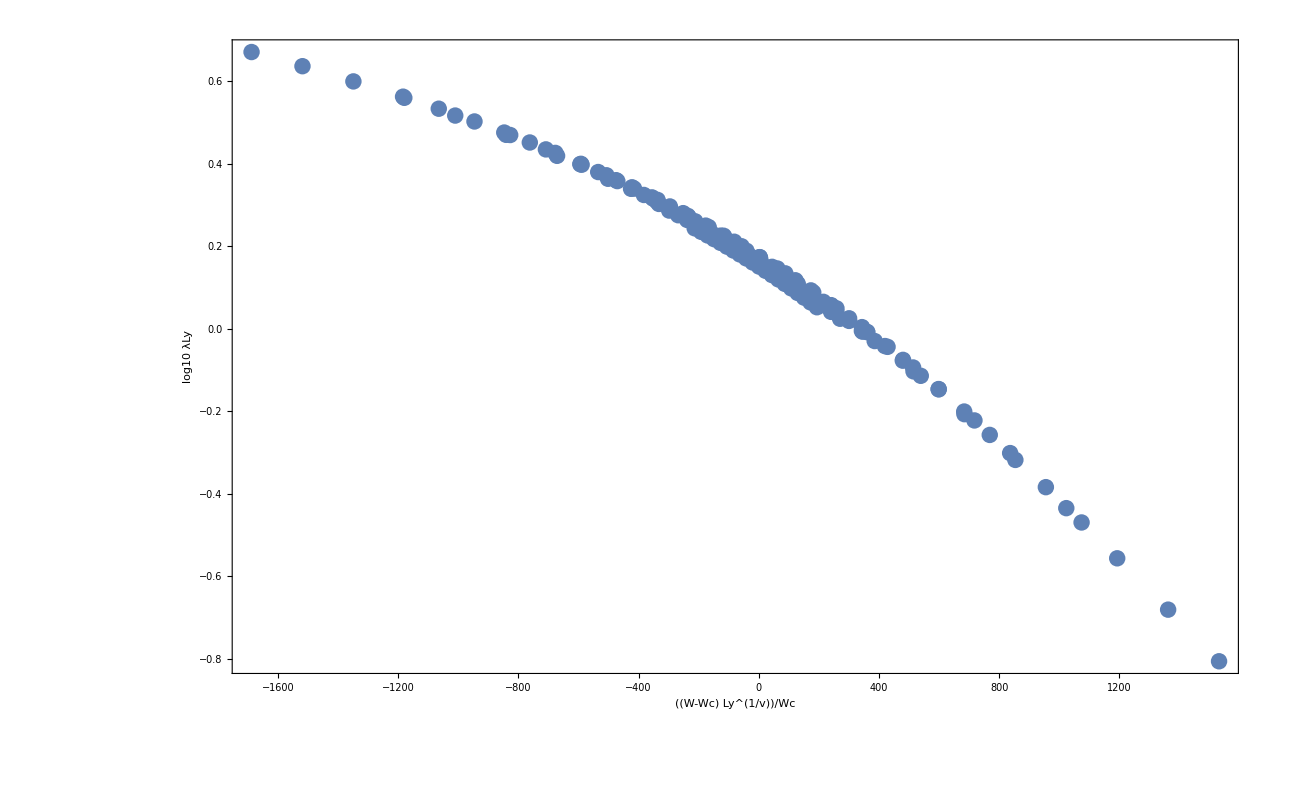

plot2.jpg

```mathematica
g01=Show[Show[ListPlot[Transpose[{((FitData⟦All,1⟧-myxc))*(FitData⟦All,2⟧)^(1/myv)/myxc,FitData⟦All,3⟧}],ImageSize->Large],Plot[ myT0+myT1*x+myT2*x^2+myT3*x^3+myT4*x^4,{x,-5,5},PlotRange->All,ImageSize->Large,PlotStyle->{Orange},AxesLabel->{(W-Wc)/(Wc)*Ly^(1/v), log10(λLy)} ]],Frame-> True,FrameLabel->{HoldForm[((W-Wc) Ly^(1/v))/Wc],HoldForm[log10 λLy]},PlotLabel->None,LabelStyle->{FontFamily->"Asap",GrayLevel[0]}]
Export["plot2.jpg",g01]
```

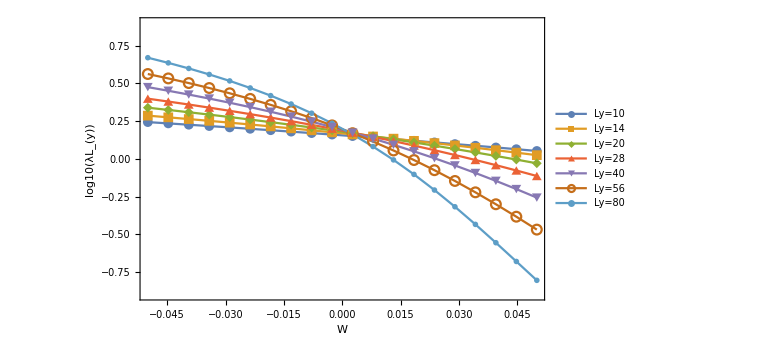

plot1.jpg

```mathematica
Line1=Transpose[{Flatten[MatrixWd[[1,start;;stop]]],Flatten[gamma[[1,start;;stop]]]}];
Line2=Transpose[{Flatten[MatrixWd[[2,start;;stop]]],Flatten[gamma[[2,start;;stop]]]}];
Line3=Transpose[{Flatten[MatrixWd[[3,start;;stop]]],Flatten[gamma[[3,start;;stop]]]}];
Line4=Transpose[{Flatten[MatrixWd[[4,start;;stop]]],Flatten[gamma[[4,start;;stop]]]}];
Line5=Transpose[{Flatten[MatrixWd[[5,start;;stop]]],Flatten[gamma[[5,start;;stop]]]}];
Line6=Transpose[{Flatten[MatrixWd[[6,start;;stop]]],Flatten[gamma[[6,start;;stop]]]}];
Line7=Transpose[{Flatten[MatrixWd[[7,start;;stop]]],Flatten[gamma[[7,start;;stop]]]}];
plottingdata=Table[{Line1,Line2,Line3,Line4,Line5,Line6,Line7}];

g00=ListLinePlot[plottingdata,PlotMarkers-> {Automatic,10},PlotStyle->Thread@{Thick,ColorData["Rainbow"]},FrameLabel->{HoldForm[W],RawBoxes[RowBox[{"log10",RowBox[{"(",SubscriptBox["λL",RowBox[{"y",")"}]]}]}]]},ImageSize->Large,Axes->True,Frame-> True,PlotRange->{All,{-0.9,0.9}},FrameStyle->{12},PlotLegends->{"Ly=10","Ly=14","Ly=20","Ly=28","Ly=40","Ly=56","Ly=80"}]
Export["plot1.jpg",g00]
```

```mathematica
(*-----------------------------------------------------------------------------END--------------------------------------------------------------------------------------------------------------*)
```

```mathematica
u0[x]=x+a2*x^2+a3*x^3;
u1[x]=0.0;
test[x,M]=T0+T1*u0[x]*M^(1/v)+ T2*(u0[x]*M^(1/v))^2
```

```mathematica
model1=T0+M^(1/v) T1 (x+a2 x^2+a3 x^3)+M^(2/v) T2 (x+a2 x^2+a3 x^3)^2
model2=T00+M^y (1+b1 x)+M^(2 y) T02 (1+b1 x)^2+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2
model3=T00+M^y (1+b1 x+b2 x^2)+M^(2 y) T02 (1+b1 x+b2 x^2)^2+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2
model4 =b0 M^y+T00+b0^2 M^(2 y) T02+M^(1/v) (x+a2 x^2)+b0 M^(1/v+y) T11 (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2
model5=T00+M^y (1+b1 x+b2 x^2)+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2+M^(2/v+y) T21 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^2+M^(3/v) T30 (x+a2 x^2+a3 x^3)^3+M^(3/v+y) T31 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^3
model6=T00+M^y (1+b1 x+b2 x^2)+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2+M^(2/v+y) T21 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^2
model7=T00+M^(1/v) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(3/v) T30 (x+a2 x^2)^3+M^y (1+b1 x+b2 x^2)+M^(1/v+y) T11 (x+a2 x^2) (1+b1 x+b2 x^2)+M^(2/v+y) T21 (x+a2 x^2)^2 (1+b1 x+b2 x^2)+M^(3/v+y) T31 (x+a2 x^2)^3 (1+b1 x+b2 x^2)
model8=T00+M^(1/v) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(1/v+y) T11 (x+a2 x^2) (1+b1 x+b2 x^2)+M^(2/v+y) T21 (x+a2 x^2)^2 (1+b1 x+b2 x^2)
model9=T00+M^y (1+b1 x)+M^(1/v) (x+a2 x^2)+M^(1/v+y) T11 (1+b1 x) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(2/v+y) T21 (1+b1 x) (x+a2 x^2)^2



curve1=NonlinearModelFit[FitData,{model1},{{v,1.0},{y,0.18},{a2,-1.0},{b1,-0.11},{T00,0.49},{T11,-0.723},{T20,-0.16},{T02,0.01}},{x,M},Weights->1/errors^2]

curve2=NonlinearModelFit[FitData,model2,{{v,1.0},{y,0.18},{a2,-1.0},{a3,0.1},{b1,-0.11},{T00,0.49},{T11,-0.723},{T20,-0.16},{T02,0.01}},{x,M},Weights->1/errors^2]
curve3=NonlinearModelFit[FitData,model3,{{v,1.0},{y,0.18},{a2,-1.0},{a3,0.1},{b1,-0.11},{b2,0.1},{T00,0.49},{T11,-0.723},{T20,-0.16},{T02,0.01}},{x,M},Weights->1/errors^2]
curve4=NonlinearModelFit[FitData,model4,{{v,1.0},{y,0.18},{a2,-1.0},{a3,0.1},{b0,1.0},{T00,0.49},{T11,-0.723},{T20,-0.16},{T02,0.01}},{x,M},Weights->1/errors^2]
curve5=NonlinearModelFit[FitData,model5,{{v,1.0},{y,0.18},{a2,-1.0},{a3,0.1},{b1,-0.11},{b2,0.1},{T00,0.49},{T11,-0.723},{T20,-0.16},{T21,0.01},{T30,0.01},{T31,0.01}},{x,M},Weights->1/errors^2]
curve6=NonlinearModelFit[FitData,model6,{{v,1.0},{y,0.18},{a2,-1.0},{a3,0.1},{b1,-0.11},{b2,0.1},{T00,0.49},{T11,-0.723},{T20,-0.16},{T21,0.01}},{x,M},Weights->1/errors^2]
curve7=NonlinearModelFit[FitData,model7,{{v,1.0},{y,0.18},{a2,-1.0},{b1,-0.11},{b2,0.1},{T00,0.49},{T11,-0.723},{T20,-0.16},{T21,0.01},{T30,0.01},{T31,0.01}},{x,M},Weights->1/errors^2]
curve8=NonlinearModelFit[FitData,model8,{{v,1.0},{y,0.18},{a2,-1.0},{b1,-0.11},{b2,0.1},{T00,0.49},{T11,-0.723},{T20,-0.16},{T21,0.01}},{x,M},Weights->1/errors^2]
curve9=NonlinearModelFit[FitData,model9,{{v,1.0},{y,0.18},{a2,-1.0},{b1,-0.11},{T00,0.49},{T11,-0.723},{T20,-0.16},{T21,0.01}},{x,M},Weights->1/errors^2]
```

T00+M^y (1+b1 x)+M^(2 y) T02 (1+b1 x)^2+M^(1/v) (x+a2 x^2)+M^(1/v+y) T11 (1+b1 x) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2

T00+M^y (1+b1 x)+M^(2 y) T02 (1+b1 x)^2+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2

T00+M^y (1+b1 x+b2 x^2)+M^(2 y) T02 (1+b1 x+b2 x^2)^2+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2

b0 M^y+T00+b0^2 M^(2 y) T02+M^(1/v) (x+a2 x^2)+b0 M^(1/v+y) T11 (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2

T00+M^y (1+b1 x+b2 x^2)+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2+M^(2/v+y) T21 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^2+M^(3/v) T30 (x+a2 x^2+a3 x^3)^3+M^(3/v+y) T31 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^3

T00+M^y (1+b1 x+b2 x^2)+M^(1/v) (x+a2 x^2+a3 x^3)+M^(1/v+y) T11 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)+M^(2/v) T20 (x+a2 x^2+a3 x^3)^2+M^(2/v+y) T21 (1+b1 x+b2 x^2) (x+a2 x^2+a3 x^3)^2

T00+M^(1/v) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(3/v) T30 (x+a2 x^2)^3+M^y (1+b1 x+b2 x^2)+M^(1/v+y) T11 (x+a2 x^2) (1+b1 x+b2 x^2)+M^(2/v+y) T21 (x+a2 x^2)^2 (1+b1 x+b2 x^2)+M^(3/v+y) T31 (x+a2 x^2)^3 (1+b1 x+b2 x^2)

T00+M^(1/v) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(1/v+y) T11 (x+a2 x^2) (1+b1 x+b2 x^2)+M^(2/v+y) T21 (x+a2 x^2)^2 (1+b1 x+b2 x^2)

T00+M^y (1+b1 x)+M^(1/v) (x+a2 x^2)+M^(1/v+y) T11 (1+b1 x) (x+a2 x^2)+M^(2/v) T20 (x+a2 x^2)^2+M^(2/v+y) T21 (1+b1 x) (x+a2 x^2)^2

FittedModel[-0.627811+(1+2.11244 x)/M^0.0062234-(0.378172 (1+«1»)^2)/M^(«21»)+M^0.453634 (x-3.52218 «1»)-2.40351 M^0.447411 (1+2.11244 x) (x-3.52218 x^2)+0.00195591 M^0.907268 (x-3.52218 x^2)^2]

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-0.43723+(1-0.390616 x)/M^0.0779399-(«19» («1»)^2)/M^(«20»)+M^(«19») (x+«1»-«19» x^3)-1.89791 M^0.668841 (1-0.390616 x) (x+1.83854 x^2-10.726 x^3)+0.00383607 M^1.49356 (x+1.83854 x^2-10.726 x^3)^2]

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-0.441544+(1-0.133729 x-4.17912 x^2)/M^0.0745266-(«1»)/(«1»)+«1»-1.81678 M^0.703519 (1-«20» x-4.17912 x^2) (x+1.36708 x^2+3.61281 x^3)+0.00428099 M^1.55609 (x+1.36708 x^2+3.61281 x^3)^2]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-0.19611-0.290078/M^0.155812+0.480233/M^0.077906-1.77758 M^0.718577 (x+1.55438 x^2)+M^0.796483 (x+1.55438 x^2)+0.00672442 M^1.59297 (x+1.55438 x^2)^2]

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-0.970072+(1-0.56628 x+1.40187 x^2)/M^0.0127286+«8»+1.93362 M^1.8778 (1-0.56628 x+1.40187 x^2) (x+4.46441 x^2+1.51071 x^3)^3]

FittedModel[-0.989478+(1-0.182373 x-7.93442 x^2)/M^0.00656761+M^(«19») (x-«19» «1»+«18» x^3)-«1»+0.284953 M^(«18») (x-«1»+4.92511 «1»)^2-0.405928 M^1.04123 (1-0.182373 x-7.93442 x^2) (x-1.46661 x^2+4.92511 x^3)^2]

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-0.977123+(1-0.775105 x-1.92674 x^2)/M^0.0107679+«8»+0.271125 M^1.90462 (1-0.775105 x-1.92674 x^2) (x+2.7814 x^2)^3]

FittedModel[-0.00745219+M^0.725349 (x-4.92196 x^2)-«20» M^(«19») («1»)^2-1.91789 M^0.650935 (x-4.92196 x^2) (1+2.80738 x+8.52503 x^2)+0.356752 M^1.37628 (x-4.92196 x^2)^2 (1+2.80738 x+8.52503 x^2)]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-1.00666+(1-0.0913865 x)/M^0.000795859+M^0.525655 (x+0.953956 x^2)-1.93149 «1»«1»«1» (x+«19» «1»)+15.7766 M^1.05131 (x+0.953956 x^2)^2-15.8105 M^1.05051 (1-0.0913865 x) (x+0.953956 x^2)^2]

```mathematica
curve1["BestFitParameters"]
curve2["BestFitParameters"]
curve3["BestFitParameters"]
curve4["BestFitParameters"]
curve5["BestFitParameters"]
curve6["BestFitParameters"]
curve7["BestFitParameters"]
curve8["BestFitParameters"]
curve9["BestFitParameters"]
```

{v→2.20442,y→-0.0062234,a2→-3.52218,b1→2.11244,T00→-0.627811,T11→-2.40351,T20→0.00195591,T02→-0.378172}

{v→1.33908,y→-0.0779399,a2→1.83854,a3→-10.726,b1→-0.390616,T00→-0.43723,T11→-1.89791,T20→0.00383607,T02→-0.577831}

{v→1.28527,y→-0.0745266,a2→1.36708,a3→3.61281,b1→-0.133729,b2→-4.17912,T00→-0.441544,T11→-1.81678,T20→0.00428099,T02→-0.569926}

{v→1.25552,y→-0.077906,a2→1.55438,a3→0.1,b0→0.480233,T00→-0.19611,T11→-3.7015,T20→0.00672442,T02→-1.2578}

{v→1.58686,y→-0.0127286,a2→4.46441,a3→1.51071,b1→-0.56628,b2→1.40187,T00→-0.970072,T11→-1.66255,T20→-3.50941,T21→3.82601,T30→-1.69752,T31→1.93362}

{v→1.90877,y→-0.00656761,a2→-1.46661,a3→4.92511,b1→-0.182373,b2→-7.93442,T00→-0.989478,T11→-1.97476,T20→0.284953,T21→-0.405928}

{v→1.56626,y→-0.0107679,a2→2.7814,b1→-0.775105,b2→-1.92674,T00→-0.977123,T11→-1.61244,T20→-0.711463,T21→0.776315,T30→-0.20246,T31→0.271125}

{v→1.37865,y→-0.0744144,a2→-4.92196,b1→2.80738,b2→8.52503,T00→-0.00745219,T11→-1.91789,T20→-0.178557,T21→0.356752}

{v→1.90239,y→-0.000795859,a2→0.953956,b1→-0.0913865,T00→-1.00666,T11→-1.93149,T20→15.7766,T21→-15.8105}

```mathematica
Collect[curve9,x]
```

FittedModel[-1.0108+(1+0.592046 x)/M^0.0143597+M^0.729306 (x+3.03032 x^2)-0.820423 «1»«1»«1» (x+«19» «1»)-0.0130646 M^1.45861 (x+3.03032 x^2)^2+0.0105853 M^1.44425 (1+0.592046 x) (x+3.03032 x^2)^2]

```mathematica
gf[f_,tests_]:=f[#]&/@tests
tests={"AdjustedRSquared","AIC","AICc","BIC","RSquared"};
Grid[Prepend[Transpose@{tests,gf[curve1,tests],gf[curve2,tests],gf[curve3,tests],gf[curve4,tests],gf[curve5,tests],gf[curve6,tests],gf[curve7,tests],gf[curve8,tests],gf[curve9,tests],gf[fitt,tests]},Style[#,Bold]&/@{"Test","Model 1","Model 2","Model 3","Model 4","Model 5","Model 6","Model 7","Model 8","Model 9"}],Alignment->Left,Dividers->{None,2->True}]
```

Test | Model 1 | Model 2 | Model 3 | Model 4 | Model 5 | Model 6 | Model 7 | Model 8 | Model 9 | 
AdjustedRSquared | 0.998151 | 0.998163 | 0.998198 | 0.997603 | 0.998303 | 0.998163 | 0.998308 | 0.998252 | 0.998176 | 0.998303
AIC | -1337.41 | -1338.63 | -1343.95 | -1251.25 | -1361.55 | -1337.63 | -1363.52 | -1354.86 | -1341.97 | -1362.56
AICc | -1336.85 | -1337.94 | -1343.11 | -1250.56 | -1360.39 | -1336.8 | -1362.53 | -1354.17 | -1341.4 | -1361.57
BIC | -1303.27 | -1300.7 | -1302.22 | -1213.32 | -1312.24 | -1295.91 | -1318. | -1316.93 | -1307.83 | -1317.04
RSquared | 0.998196 | 0.998214 | 0.998253 | 0.997669 | 0.998365 | 0.998219 | 0.998365 | 0.9983 | 0.998221 | 0.99836

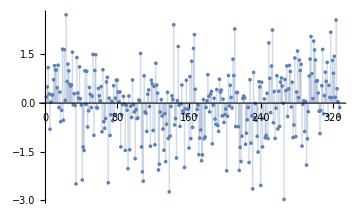
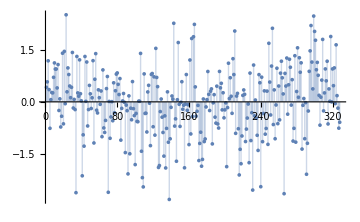
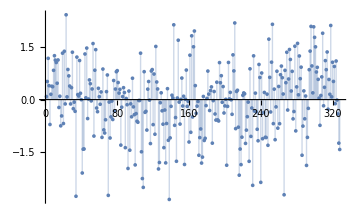
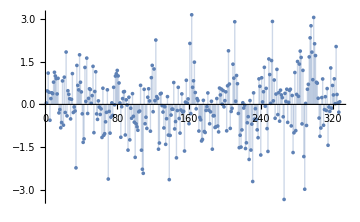

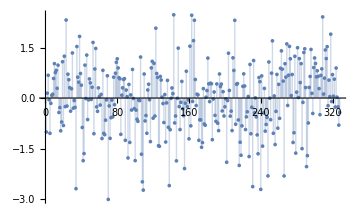
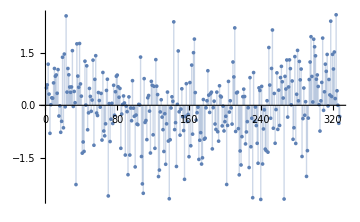
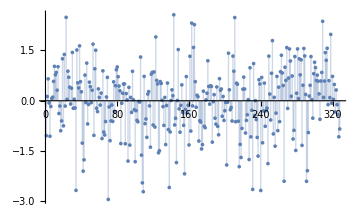
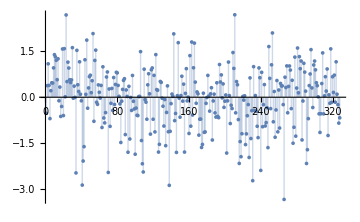

```mathematica
res1=curve1["StandardizedResiduals"];
res2=curve2["StandardizedResiduals"];
res3=curve3["StandardizedResiduals"];
res4=curve4["StandardizedResiduals"];
res5=curve5["StandardizedResiduals"];
res6=curve6["StandardizedResiduals"];
res7=curve7["StandardizedResiduals"];
res8=curve8["StandardizedResiduals"];
res9=curve9["StandardizedResiduals"];
Row[{ListPlot[res1,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res2,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res3,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res4,PlotRange->All,Filling->Axis,ImageSize->Medium]}]
Row[{ListPlot[res5,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res6,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res7,PlotRange->All,Filling->Axis,ImageSize->Medium],ListPlot[res8,PlotRange->All,Filling->Axis,ImageSize->Medium]}]
Row[{ListPlot[res9,PlotRange->All,Filling->Axis,ImageSize->Medium]}]
```

```mathematica
-Graphics-5.0-Graphics--Graphics-
```

-Graphics-

```mathematica
{Expectation[x,x\[Distributed]EmpiricalDistribution[res1]],Expectation[x,x\[Distributed]EmpiricalDistribution[res2]],Expectation[x,x\[Distributed]EmpiricalDistribution[res3]],Expectation[x,x\[Distributed]EmpiricalDistribution[res4]],Expectation[x,x\[Distributed]EmpiricalDistribution[res5]],Expectation[x,x\[Distributed]EmpiricalDistribution[res6]],Expectation[x,x\[Distributed]EmpiricalDistribution[res7]],Expectation[x,x\[Distributed]EmpiricalDistribution[res8]],Expectation[x,x\[Distributed]EmpiricalDistribution[res9]]}
```

{-0.0225458,-0.0173447,-0.0231262,0.00547743,-0.0207056,-0.0247081,-0.0205982,-0.0385684,-0.0337182}

```mathematica
h1=PearsonChiSquareTest[res1,Automatic,"HypothesisTestData"];
h2=PearsonChiSquareTest[res2,Automatic,"HypothesisTestData"];
h3=PearsonChiSquareTest[res3,Automatic,"HypothesisTestData"];
h4=PearsonChiSquareTest[res4,Automatic,"HypothesisTestData"];
h5=PearsonChiSquareTest[res5,Automatic,"HypothesisTestData"];
h6=PearsonChiSquareTest[res6,Automatic,"HypothesisTestData"];
h7=PearsonChiSquareTest[res7,Automatic,"HypothesisTestData"];
h8=PearsonChiSquareTest[res8,Automatic,"HypothesisTestData"];
h9=PearsonChiSquareTest[res9,Automatic,"HypothesisTestData"];
{h1["TestDataTable"],h2["TestDataTable"],h3["TestDataTable"],h4["TestDataTable"]}
{h5["TestDataTable"],h6["TestDataTable"],h7["TestDataTable"],h8["TestDataTable"],h9["TestDataTable"]}
```

{ | Statistic | P-Value
Pearson χ^2 | 15.2988 | 0.64136, | Statistic | P-Value
Pearson χ^2 | 18.8841 | 0.39899, | Statistic | P-Value
Pearson χ^2 | 21.4451 | 0.257554, | Statistic | P-Value
Pearson χ^2 | 18.1159 | 0.448045}

{ | Statistic | P-Value
Pearson χ^2 | 20.5488 | 0.302785, | Statistic | P-Value
Pearson χ^2 | 18.2439 | 0.439697, | Statistic | P-Value
Pearson χ^2 | 24.1341 | 0.150682, | Statistic | P-Value
Pearson χ^2 | 24.3902 | 0.142654, | Statistic | P-Value
Pearson χ^2 | 22.3415 | 0.217177}

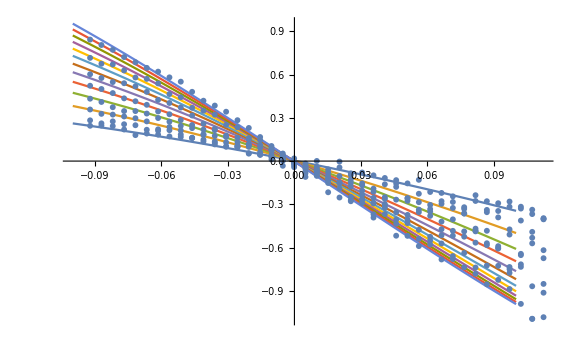

```mathematica
Show[Plot[Evaluate[Table[curve4["BestFit"],{M,10,120,10}]],{x,-0.1,0.1},PlotRange->All,ImageSize->Large],ListPlot[Transpose[{FitData⟦All,1⟧,FitData⟦All,3⟧}]]]
```

```mathematica
curve4["ParameterTable"]
```

General::munfl: Exp[-8229.96] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
v | 1.25552 | 0.0522082 | 24.0483 | 1.26994×10^-73
y | -0.077906 | 0.00192603 | -40.449 | 1.26066×10^-127
a2 | 1.55438 | 0.133374 | 11.6543 | 2.17688×10^-26
a3 | 0.1 | 3.53076×10^-14 | 2.83225×10^12 | 0.
b0 | 0.480233 | 1.45937 | 0.329069 | 0.74232
T00 | -0.19611 | 0.562837 | -0.348431 | 0.727746
T11 | -3.7015 | 11.2357 | -0.329442 | 0.742038
T20 | 0.00672442 | 0.00205915 | 3.26563 | 0.00121093
T02 | -1.2578 | 3.55819 | -0.353495 | 0.723951

```mathematica
Collect[model4,x]
```

b0 M^y+T00+b0^2 M^(2 y) T02+(M^(1/v)+b0 M^(1/v+y) T11) x+(a2 M^(1/v)+a2 b0 M^(1/v+y) T11+M^(2/v) T20) x^2+2 a2 M^(2/v) T20 x^3+a2^2 M^(2/v) T20 x^4

```mathematica
curve1["Data"]
```